```mathematica
(*(c)dUmon, ELI, 01NOV2021*)
```

```mathematica
(*SOURCE: 60Co*)
```

3842509068

3842532402

23334.

1.93103×10^8

9.62885×10^8

Activity  (Bq) 41267.3

Duration (s) 23334.

Activity Sum  9.62932×10^8

Int Sum  962884704.

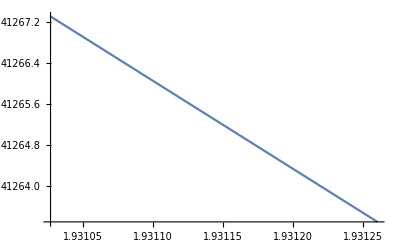

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2015,08,24,12,00}];
TH2=1925.28*24*3600;(*NNDC, days -> seconds*)
A0=92.27*10^3;(*Bq*)
λ:=Log[2]/TH2;


Tstart=AbsoluteTime[{2021,10,6,11,37,48}]
Tstop=AbsoluteTime[{2021,10,6,18,6,42}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```

```mathematica
(*SOURCE: 54Mn*)
```

3845618755

3845619347

592.

2.203×10^7

1.73493×10^8

Activity  (Bq) 293065.

Duration (s) 592.

Activity Sum  1.73495×10^8

Int Sum  173493300.

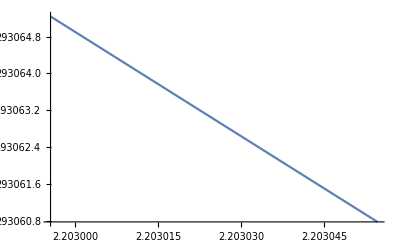

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2021,03,01,12,00}];
TH2=312.2*24*3600;(*NNDC, days -> seconds*)
A0=516.2*10^3;(*Bq*)
λ:=Log[2]/TH2;


Tstart=AbsoluteTime[{2021,11,11,11,25,55}]
Tstop=AbsoluteTime[{2021,11,11,11,35,47}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```

```mathematica
(*SOURCE: 133Ba*)
```

3845622370

3845623213

843.

2.20336×10^7

3.1402×10^6

Activity  (Bq) 3725.04

Duration (s) 843.

Activity Sum  3.14021×10^6

Int Sum  3140204.

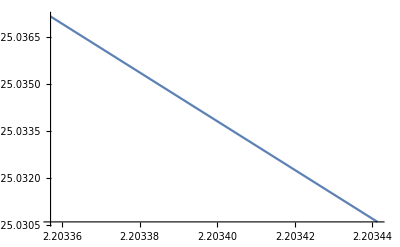

```mathematica
Clear["Global`*"]
ZeroTime=AbsoluteTime[{2021,03,01,12,00}];
TH2=10.551*365*24*3600;(*NNDC, seconds*)
A0=3.9*10^3;(*Bq*)
λ:=Log[2]/TH2;


Tstart=AbsoluteTime[{2021,11,11,12,26,10}]
Tstop=AbsoluteTime[{2021,11,11,12,40,13}]
duration=N[(Tstop-Tstart)]

DecayTime=N[(Tstart-ZeroTime)](*s*)
AA[x_]:=A0*Exp[(-1)*λ*x];
ActivityNow=AA[DecayTime];
ActivitySum=ActivityNow*duration;
SumInt=Integrate[AA[x],{x,DecayTime,(DecayTime+duration)}]
Print["Activity  (Bq) ",AA[DecayTime]]
Print["Duration (s) ",duration]
Print["Activity Sum  ",ActivitySum]
Print["Int Sum  ",DecimalForm[SumInt]]
Plot[{AA[x]},{x,DecayTime,DecayTime+duration}]
```